```mathematica
TriangularGridGraph[{wide_Integer?Positive,high_Integer?Positive},opts:OptionsPattern[Graph]]:= Module[{cells,edges, vertices}, 
cells=Flatten[Table[CirclePoints[{√3(2j+k-2 ),3k-2},{2,π/2},3],{j,wide},{k,high}],1];
edges=Union[Sort/@Flatten[Partition[#,2,1,1]&/@cells,1]];
vertices=Union[Flatten[edges,1]];
IndexGraph[Graph[UndirectedEdge@@@edges,opts, VertexCoordinates->Thread[vertices-> vertices]]]]
```

```mathematica
Table[CirclePoints[{√3(2j+k-2 ),3k-2},{2,π/2},3],{j,3},{k,4}]
```

{{{{√3,3},{0,0},{2 √3,0}},{{2 √3,6},{√3,3},{3 √3,3}},{{3 √3,9},{2 √3,6},{4 √3,6}},{{4 √3,12},{3 √3,9},{5 √3,9}}},{{{3 √3,3},{2 √3,0},{4 √3,0}},{{4 √3,6},{3 √3,3},{5 √3,3}},{{5 √3,9},{4 √3,6},{6 √3,6}},{{6 √3,12},{5 √3,9},{7 √3,9}}},{{{5 √3,3},{4 √3,0},{6 √3,0}},{{6 √3,6},{5 √3,3},{7 √3,3}},{{7 √3,9},{6 √3,6},{8 √3,6}},{{8 √3,12},{7 √3,9},{9 √3,9}}}}

```mathematica
Flatten[Table[CirclePoints[{√3(2j+k-2 ),3k-2},{2,π/2},3],{j,3},{k,4}],1]
```

{{{√3,3},{0,0},{2 √3,0}},{{2 √3,6},{√3,3},{3 √3,3}},{{3 √3,9},{2 √3,6},{4 √3,6}},{{4 √3,12},{3 √3,9},{5 √3,9}},{{3 √3,3},{2 √3,0},{4 √3,0}},{{4 √3,6},{3 √3,3},{5 √3,3}},{{5 √3,9},{4 √3,6},{6 √3,6}},{{6 √3,12},{5 √3,9},{7 √3,9}},{{5 √3,3},{4 √3,0},{6 √3,0}},{{6 √3,6},{5 √3,3},{7 √3,3}},{{7 √3,9},{6 √3,6},{8 √3,6}},{{8 √3,12},{7 √3,9},{9 √3,9}}}

```mathematica
Flatten[Partition[#,2,1,1]&/@Flatten[Table[CirclePoints[{√3(2j+k-2 ),3k-2},{2,π/2},3],{j,3},{k,4}],1],1]
```

{{{√3,3},{0,0}},{{0,0},{2 √3,0}},{{2 √3,0},{√3,3}},{{2 √3,6},{√3,3}},{{√3,3},{3 √3,3}},{{3 √3,3},{2 √3,6}},{{3 √3,9},{2 √3,6}},{{2 √3,6},{4 √3,6}},{{4 √3,6},{3 √3,9}},{{4 √3,12},{3 √3,9}},{{3 √3,9},{5 √3,9}},{{5 √3,9},{4 √3,12}},{{3 √3,3},{2 √3,0}},{{2 √3,0},{4 √3,0}},{{4 √3,0},{3 √3,3}},{{4 √3,6},{3 √3,3}},{{3 √3,3},{5 √3,3}},{{5 √3,3},{4 √3,6}},{{5 √3,9},{4 √3,6}},{{4 √3,6},{6 √3,6}},{{6 √3,6},{5 √3,9}},{{6 √3,12},{5 √3,9}},{{5 √3,9},{7 √3,9}},{{7 √3,9},{6 √3,12}},{{5 √3,3},{4 √3,0}},{{4 √3,0},{6 √3,0}},{{6 √3,0},{5 √3,3}},{{6 √3,6},{5 √3,3}},{{5 √3,3},{7 √3,3}},{{7 √3,3},{6 √3,6}},{{7 √3,9},{6 √3,6}},{{6 √3,6},{8 √3,6}},{{8 √3,6},{7 √3,9}},{{8 √3,12},{7 √3,9}},{{7 √3,9},{9 √3,9}},{{9 √3,9},{8 √3,12}}}

```mathematica
Sort/@Flatten[Partition[#,2,1,1]&/@Flatten[Table[CirclePoints[{√3(2j+k-2 ),3k-2},{2,π/2},3],{j,3},{k,4}],1],1]
```

{{{0,0},{√3,3}},{{0,0},{2 √3,0}},{{√3,3},{2 √3,0}},{{√3,3},{2 √3,6}},{{√3,3},{3 √3,3}},{{2 √3,6},{3 √3,3}},{{2 √3,6},{3 √3,9}},{{2 √3,6},{4 √3,6}},{{3 √3,9},{4 √3,6}},{{3 √3,9},{4 √3,12}},{{3 √3,9},{5 √3,9}},{{4 √3,12},{5 √3,9}},{{2 √3,0},{3 √3,3}},{{2 √3,0},{4 √3,0}},{{3 √3,3},{4 √3,0}},{{3 √3,3},{4 √3,6}},{{3 √3,3},{5 √3,3}},{{4 √3,6},{5 √3,3}},{{4 √3,6},{5 √3,9}},{{4 √3,6},{6 √3,6}},{{5 √3,9},{6 √3,6}},{{5 √3,9},{6 √3,12}},{{5 √3,9},{7 √3,9}},{{6 √3,12},{7 √3,9}},{{4 √3,0},{5 √3,3}},{{4 √3,0},{6 √3,0}},{{5 √3,3},{6 √3,0}},{{5 √3,3},{6 √3,6}},{{5 √3,3},{7 √3,3}},{{6 √3,6},{7 √3,3}},{{6 √3,6},{7 √3,9}},{{6 √3,6},{8 √3,6}},{{7 √3,9},{8 √3,6}},{{7 √3,9},{8 √3,12}},{{7 √3,9},{9 √3,9}},{{8 √3,12},{9 √3,9}}}

```mathematica
Flatten[Sort/@Flatten[Partition[#,2,1,1]&/@Flatten[Table[CirclePoints[{√3(2j+k-2 ),3k-2},{2,π/2},3],{j,3},{k,4}],1],1],1]
```

{{0,0},{√3,3},{0,0},{2 √3,0},{√3,3},{2 √3,0},{√3,3},{2 √3,6},{√3,3},{3 √3,3},{2 √3,6},{3 √3,3},{2 √3,6},{3 √3,9},{2 √3,6},{4 √3,6},{3 √3,9},{4 √3,6},{3 √3,9},{4 √3,12},{3 √3,9},{5 √3,9},{4 √3,12},{5 √3,9},{2 √3,0},{3 √3,3},{2 √3,0},{4 √3,0},{3 √3,3},{4 √3,0},{3 √3,3},{4 √3,6},{3 √3,3},{5 √3,3},{4 √3,6},{5 √3,3},{4 √3,6},{5 √3,9},{4 √3,6},{6 √3,6},{5 √3,9},{6 √3,6},{5 √3,9},{6 √3,12},{5 √3,9},{7 √3,9},{6 √3,12},{7 √3,9},{4 √3,0},{5 √3,3},{4 √3,0},{6 √3,0},{5 √3,3},{6 √3,0},{5 √3,3},{6 √3,6},{5 √3,3},{7 √3,3},{6 √3,6},{7 √3,3},{6 √3,6},{7 √3,9},{6 √3,6},{8 √3,6},{7 √3,9},{8 √3,6},{7 √3,9},{8 √3,12},{7 √3,9},{9 √3,9},{8 √3,12},{9 √3,9}}

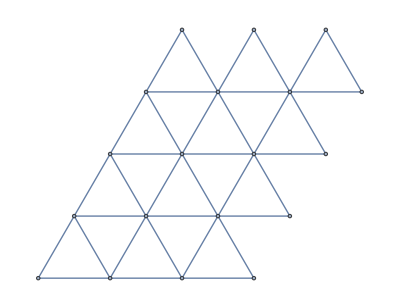

```mathematica
IndexGraph[Graph[UndirectedEdge@@@Sort/@Flatten[Partition[#,2,1,1]&/@Flatten[Table[CirclePoints[{√3(2j+k-2 ),3k-2},{2,π/2},3],{j,3},{k,4}],1],1],VertexCoordinates->Thread[Flatten[Sort/@Flatten[Partition[#,2,1,1]&/@Flatten[Table[CirclePoints[{√3(2j+k-2 ),3k-2},{2,π/2},3],{j,3},{k,4}],1],1],1]-> Flatten[Sort/@Flatten[Partition[#,2,1,1]&/@Flatten[Table[CirclePoints[{√3(2j+k-2 ),3k-2},{2,π/2},3],{j,3},{k,4}],1],1],1]]]]
```

```mathematica
FindSequenceFunction[{1,2,4,7,10,14,18,23,28,34,40}]
```

```mathematica
InputForm[FindSequenceFunction[{1,2,4,7,10,14,18,23,28,34,40}]]
```

DifferenceRoot[Function[{y, n}, {7 + 5*n + (1 - n)*y[n] - 2*y[1 + n] + (-3 + n)*y[2 + n] == 0, y[1] == 1, y[2] == 2, 
   y[3] == 4, y[4] == 7, y[5] == 10}]]

```mathematica
FindSequenceFunction[{1,2,4,7,10,14,18,23,28,34,40,47,54}]
```

```mathematica
InputForm[FindSequenceFunction[{1,2,4,7,10,14,18,23,28,34,40,47,54}]]
```

DifferenceRoot[Function[{y, n}, {2 - 5*n - n^2 + 2*y[n] + 2*y[1 + n] == 0, y[1] == 1, y[2] == 2}]]

```mathematica
InputForm[FindSequenceFunction[{1,2,4,7,10,14,18,23,28,34,40,47,54,62}]]
```

DifferenceRoot[Function[{y, n}, {2 - 5*n - n^2 + 2*y[n] + 2*y[1 + n] == 0, y[1] == 1, y[2] == 2}]]

```mathematica
FindSequenceFunction[{1,2,4,7,10,14,18,23,28,34,40,47,54}]===FindSequenceFunction[{1,2,4,7,10,14,18,23,28,34,40,47,54,62}]
```

True

```mathematica
FunctionExpand[FindSequenceFunction[{1,2,4,7,10,14,18,23,28,34,40,47,54}],n]
```

```mathematica
FindSequenceFunction[{1,3,6,12,20,30,42,56,72}]
```

3+[#1]&

```mathematica
FindSequenceFunction[{1,3,6,12,20,30,42,56,72,87}]
```

FindSequenceFunction[{1,3,6,12,20,30,42,56,72,87}]

```mathematica
FindSequenceFunction[{1,3,6,12,20,30,42,56,72,87,102,117,132}]
```

FindSequenceFunction[{1,3,6,12,20,30,42,56,72,87,102,117,132}]

```mathematica
FindSequenceFunction[{70,85,100,115,130,145,160}]
```

5 (11+3 #1)&

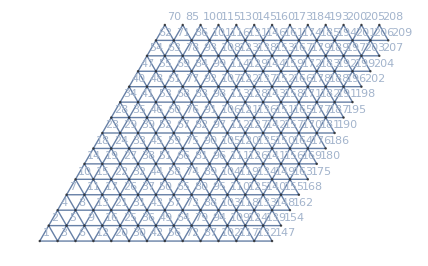

```mathematica
TriangularGridGraph[{13,14},VertexLabels->Automatic]
```

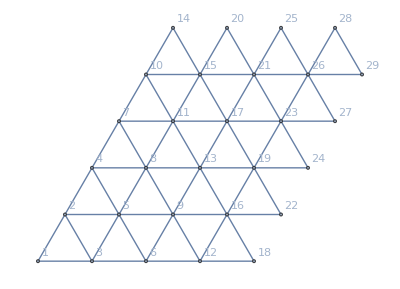

```mathematica
TriangularGridGraph[{3+1,4+1},VertexLabels->Automatic]
```

```mathematica
VertexCoordinateList[-Graphics-]
```

{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{5 √3,15},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{7 √3,15},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{9 √3,15},{10 √3,12},{11 √3,9},{11 √3,15},{12 √3,12}}

```mathematica
PositionLargest[VertexCoordinateList[-Graphics-],1,Order[Last[#1],Last[#2]]&]
```

{{14,20,25,28}}

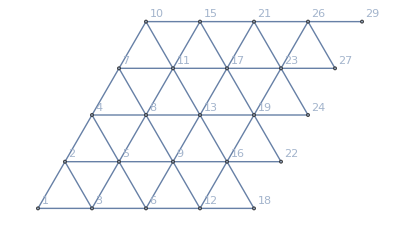

```mathematica
VertexDelete[-Graphics-,Flatten[PositionLargest[VertexCoordinateList[-Graphics-],1,Order[Last[#1],Last[#2]]&]]]
```

```mathematica
TriangularGridGraphFunction[input_]:=Module[{vertexCoordinates,triangularGridGraph,vertices, vertexCoordinatesToVerticesAssociation,topPartDeletedGraph,topPartDeletedVertexCoordinateList,vertexCoordinatesToDelete,flattenedCoordinatesToDelete,vertexCoordinatesToKeep,vertexCoordinatesToKeepList,subGraph,verticesToKeep},triangularGridGraph=TriangularGridGraph[input+1];

vertexCoordinates=VertexCoordinateList[triangularGridGraph];

vertices=VertexList[triangularGridGraph];topPartDeletedGraph=VertexDelete[triangularGridGraph,Flatten[PositionLargest[vertexCoordinates,1,Order[Last[#1],Last[#2]]&]]];topPartDeletedVertexCoordinateList=VertexCoordinateList[topPartDeletedGraph];

vertexCoordinatesToDelete=TakeLargestBy[First,1]/@GroupBy[Last][topPartDeletedVertexCoordinateList];
flattenedCoordinatesToDelete=Flatten[Values[vertexCoordinatesToDelete],1];

vertexCoordinatesToKeep=DeleteElements[topPartDeletedVertexCoordinateList,flattenedCoordinatesToDelete];

vertexCoordinatesToKeepList=Flatten@Table[Position[vertexCoordinatesToKeep,element],{element,vertexCoordinatesToKeep}];

vertexCoordinatesToVerticesAssociation=AssociationThread[vertexCoordinates->vertices];verticesToKeep=Lookup[vertexCoordinatesToVerticesAssociation,Catenate[Values[Most/@SortBy[First]/@GroupBy[Last][vertexCoordinates]]]];
subGraph=Echo@Subgraph[topPartDeletedGraph,verticesToKeep];AssociationThread[ToString/@Unevaluated/@Unevaluated[{vertexCoordinates,triangularGridGraph,vertices, vertexCoordinatesToVerticesAssociation,topPartDeletedGraph,topPartDeletedVertexCoordinateList,vertexCoordinatesToDelete,flattenedCoordinatesToDelete,vertexCoordinatesToKeep,vertexCoordinatesToKeepList,subGraph,verticesToKeep}]->{vertexCoordinates,triangularGridGraph,vertices, vertexCoordinatesToVerticesAssociation,topPartDeletedGraph,topPartDeletedVertexCoordinateList,vertexCoordinatesToDelete,flattenedCoordinatesToDelete,vertexCoordinatesToKeep,vertexCoordinatesToKeepList,subGraph,verticesToKeep}]]
```

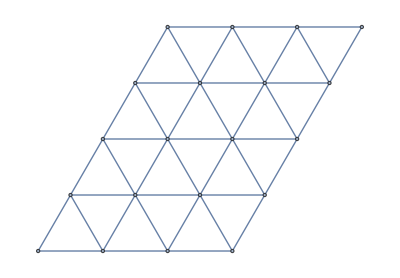

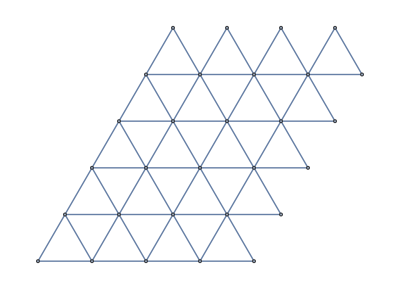
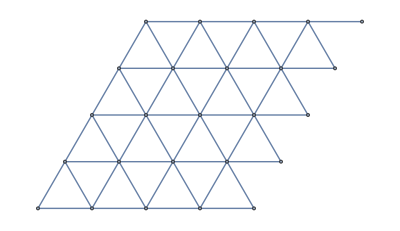
<|vertexCoordinates$152002→{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{5 √3,15},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{7 √3,15},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{9 √3,15},{10 √3,12},{11 √3,9},{11 √3,15},{12 √3,12}},triangularGridGraph$152002→-Graphics-,vertices$152002→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29},vertexCoordinatesToVerticesAssociation$152002→<|{0,0}→1,{√3,3}→2,{2 √3,0}→3,{2 √3,6}→4,{3 √3,3}→5,{4 √3,0}→6,{3 √3,9}→7,{4 √3,6}→8,{5 √3,3}→9,{4 √3,12}→10,{5 √3,9}→11,{6 √3,0}→12,{6 √3,6}→13,{5 √3,15}→14,{6 √3,12}→15,{7 √3,3}→16,{7 √3,9}→17,{8 √3,0}→18,{8 √3,6}→19,{7 √3,15}→20,{8 √3,12}→21,{9 √3,3}→22,{9 √3,9}→23,{10 √3,6}→24,{9 √3,15}→25,{10 √3,12}→26,{11 √3,9}→27,{11 √3,15}→28,{12 √3,12}→29|>,topPartDeletedGraph$152002→-Graphics-,topPartDeletedVertexCoordinateList$152002→{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{10 √3,12},{11 √3,9},{12 √3,12}},vertexCoordinatesToDelete$152002→<|0→{{8 √3,0}},3→{{9 √3,3}},6→{{10 √3,6}},9→{{11 √3,9}},12→{{12 √3,12}}|>,flattenedCoordinatesToDelete$152002→{{8 √3,0},{9 √3,3},{10 √3,6},{11 √3,9},{12 √3,12}},vertexCoordinatesToKeep$152002→{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,6},{8 √3,12},{9 √3,9},{10 √3,12}},vertexCoordinatesToKeepList$152002→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},subGraph$152002→-Graphics-,verticesToKeep$152002→{1,3,6,12,2,5,9,16,4,8,13,19,7,11,17,23,10,15,21,26,14,20,25}|>

```mathematica
TriangularGridGraphFunction[{3,4}]
```

```mathematica
GroupBy[Last][{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{10 √3,12},{11 √3,9},{12 √3,12}}]
```

<|0→{{0,0},{2 √3,0},{4 √3,0},{6 √3,0},{8 √3,0}},3→{{√3,3},{3 √3,3},{5 √3,3},{7 √3,3},{9 √3,3}},6→{{2 √3,6},{4 √3,6},{6 √3,6},{8 √3,6},{10 √3,6}},9→{{3 √3,9},{5 √3,9},{7 √3,9},{9 √3,9},{11 √3,9}},12→{{4 √3,12},{6 √3,12},{8 √3,12},{10 √3,12},{12 √3,12}}|>

```mathematica
Most/@SortBy[First]/@GroupBy[Last][{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{10 √3,12},{11 √3,9},{12 √3,12}}]
```

<|0→{{0,0},{2 √3,0},{4 √3,0},{6 √3,0}},3→{{√3,3},{3 √3,3},{5 √3,3},{7 √3,3}},6→{{2 √3,6},{4 √3,6},{6 √3,6},{8 √3,6}},9→{{3 √3,9},{5 √3,9},{7 √3,9},{9 √3,9}},12→{{4 √3,12},{6 √3,12},{8 √3,12},{10 √3,12}}|>

```mathematica
Catenate[Values[Most/@SortBy[First]/@GroupBy[Last][{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{10 √3,12},{11 √3,9},{12 √3,12}}]]]
```

{{0,0},{2 √3,0},{4 √3,0},{6 √3,0},{√3,3},{3 √3,3},{5 √3,3},{7 √3,3},{2 √3,6},{4 √3,6},{6 √3,6},{8 √3,6},{3 √3,9},{5 √3,9},{7 √3,9},{9 √3,9},{4 √3,12},{6 √3,12},{8 √3,12},{10 √3,12}}

```mathematica
Lookup[<|{0,0}->1,{√3,3}->2,{2 √3,0}->3,{2 √3,6}->4,{3 √3,3}->5,{4 √3,0}->6,{3 √3,9}->7,{4 √3,6}->8,{5 √3,3}->9,{4 √3,12}->10,{5 √3,9}->11,{6 √3,0}->12,{6 √3,6}->13,{5 √3,15}->14,{6 √3,12}->15,{7 √3,3}->16,{7 √3,9}->17,{8 √3,0}->18,{8 √3,6}->19,{7 √3,15}->20,{8 √3,12}->21,{9 √3,3}->22,{9 √3,9}->23,{10 √3,6}->24,{9 √3,15}->25,{10 √3,12}->26,{11 √3,9}->27,{11 √3,15}->28,{12 √3,12}->29|>,{{0,0},{2 √3,0},{4 √3,0},{6 √3,0},{√3,3},{3 √3,3},{5 √3,3},{7 √3,3},{2 √3,6},{4 √3,6},{6 √3,6},{8 √3,6},{3 √3,9},{5 √3,9},{7 √3,9},{9 √3,9},{4 √3,12},{6 √3,12},{8 √3,12},{10 √3,12}}]
```

{1,3,6,12,2,5,9,16,4,8,13,19,7,11,17,23,10,15,21,26}

```mathematica
Subgraph[-Graphics-,{1,3,6,12,2,5,9,16,4,8,13,19,7,11,17,23,10,15,21,26}]
```

-Graphics-

```mathematica
{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{10 √3,12},{11 √3,9},{12 √3,12}}
```

{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{10 √3,12},{11 √3,9},{12 √3,12}}

```mathematica
DeleteElements[{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{10 √3,12},{11 √3,9},{12 √3,12}},{{8 √3,0},{9 √3,3},{10 √3,6},{11 √3,9},{12 √3,12}}]
```

{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,6},{8 √3,12},{9 √3,9},{10 √3,12}}

```mathematica
Table[Position[{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{5 √3,15},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{7 √3,15},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{9 √3,15},{10 √3,12},{11 √3,9},{11 √3,15},{12 √3,12}},element],{element,{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,6},{8 √3,12},{9 √3,9},{10 √3,12}}}]
```

{{{1}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{11}},{{12}},{{13}},{{15}},{{16}},{{17}},{{19}},{{21}},{{23}},{{26}}}

```mathematica
Flatten[Table[Position[{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{5 √3,15},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{7 √3,15},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{9 √3,15},{10 √3,12},{11 √3,9},{11 √3,15},{12 √3,12}},element],{element,{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,6},{8 √3,12},{9 √3,9},{10 √3,12}}}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,15,16,17,19,21,23,26}

```mathematica
Values[<|0->{{8 √3,0}},3->{{9 √3,3}},6->{{10 √3,6}},9->{{11 √3,9}},12->{{12 √3,12}}|>]
```

{{{8 √3,0}},{{9 √3,3}},{{10 √3,6}},{{11 √3,9}},{{12 √3,12}}}

```mathematica
Flatten[Values[<|0->{{8 √3,0}},3->{{9 √3,3}},6->{{10 √3,6}},9->{{11 √3,9}},12->{{12 √3,12}}|>],1]
```

{{8 √3,0},{9 √3,3},{10 √3,6},{11 √3,9},{12 √3,12}}

```mathematica
GroupBy[Last][{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{10 √3,12},{11 √3,9},{12 √3,12}}]
```

<|0→{{0,0},{2 √3,0},{4 √3,0},{6 √3,0},{8 √3,0}},3→{{√3,3},{3 √3,3},{5 √3,3},{7 √3,3},{9 √3,3}},6→{{2 √3,6},{4 √3,6},{6 √3,6},{8 √3,6},{10 √3,6}},9→{{3 √3,9},{5 √3,9},{7 √3,9},{9 √3,9},{11 √3,9}},12→{{4 √3,12},{6 √3,12},{8 √3,12},{10 √3,12},{12 √3,12}}|>

```mathematica
TakeLargestBy[First,1]/@GroupBy[Last][{{0,0},{√3,3},{2 √3,0},{2 √3,6},{3 √3,3},{4 √3,0},{3 √3,9},{4 √3,6},{5 √3,3},{4 √3,12},{5 √3,9},{6 √3,0},{6 √3,6},{6 √3,12},{7 √3,3},{7 √3,9},{8 √3,0},{8 √3,6},{8 √3,12},{9 √3,3},{9 √3,9},{10 √3,6},{10 √3,12},{11 √3,9},{12 √3,12}}]
```

<|0→{{8 √3,0}},3→{{9 √3,3}},6→{{10 √3,6}},9→{{11 √3,9}},12→{{12 √3,12}}|>

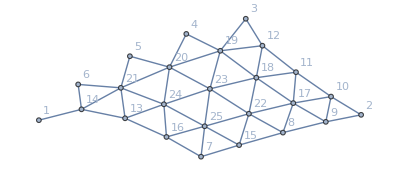

```mathematica
Graph[CanonicalGraph[VertexDelete[-Graphics-,Flatten[PositionLargest[VertexCoordinateList[-Graphics-],1,Order[Last[#1],Last[#2]]&]]]],VertexLabels->Automatic]
```

```mathematica
Sort[{1,6,5,4,3}]
```

{1,3,4,5,6}

```mathematica
FindSequenceFunction[{1,3,4,5,6}]
```

FindSequenceFunction[{1,3,4,5,6}]

```mathematica
FindSequenceFunction[{18,22,24,27,29}]
```

FindSequenceFunction[{18,22,24,27,29}]

```mathematica
Position[]
```

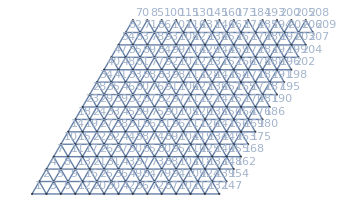
```mathematica
CanonicalGraph[-Graphics-]
```

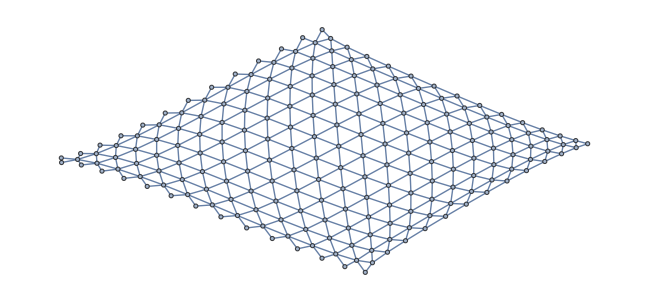

```mathematica
IncidenceList[TriangularGridGraph[{3,4}],_]
```

{1<->2,1<->3,2<->3,2<->4,2<->5,3<->5,3<->6,4<->5,4<->7,4<->8,5<->6,5<->8,5<->9,7<->8,7<->10,7<->11,6<->9,6<->12,8<->9,8<->11,8<->13,10<->11,9<->12,9<->13,9<->14,11<->13,11<->15,11<->16,13<->14,13<->16,13<->17,15<->16,16<->17,16<->18,16<->19,18<->19}

```mathematica
Normal@IncidenceMatrix[TriangularGridGraph[{3,4}]]
```

{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}

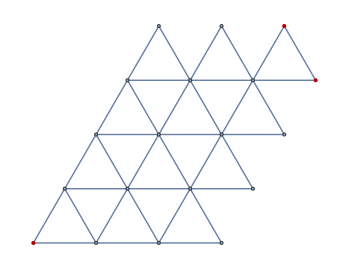

```mathematica
HighlightGraph[-Graphics-,GraphPeriphery[-Graphics-]]
```

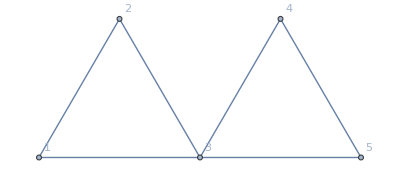

```mathematica
TriangularGridGraph[{2,1},VertexLabels->Automatic]
```

```mathematica
VertexDegree[-Graphics-]
```

{2,2,4,2,2}

```mathematica
nearestFunction[{3 √3,3},6]
```

{{3 √3,3},{√3,3},{2 √3,0},{4 √3,0},{0,0}}

```mathematica
GroupBy[EuclideanDistance[#,{3 √3,3}]&][nearestFunction[{3 √3,3},6]]
```

<|0→{{3 √3,3}},2 √3→{{√3,3},{2 √3,0},{4 √3,0}},6→{{0,0}}|>

```mathematica
Rest[GroupBy[EuclideanDistance[#,{3 √3,3}]&][nearestFunction[{3 √3,3},6]]]
```

<|2 √3→{{√3,3},{2 √3,0},{4 √3,0}},6→{{0,0}}|>

```mathematica
First[Rest[GroupBy[EuclideanDistance[#,{3 √3,3}]&][nearestFunction[{3 √3,3},6]]]]
```

{{√3,3},{2 √3,0},{4 √3,0}}

```mathematica
Position[VertexCoordinateList[-Graphics-],{√3,3}]
```

{{2}}

```mathematica
Module[{vertexCoordinateList,nearestFunction},vertexCoordinateList=VertexCoordinateList[-Graphics-];nearestFunction=Nearest[vertexCoordinateList];]
```

```mathematica
AssociationThread[VertexList[-Graphics-]->VertexCoordinateList[-Graphics-]]
```

<|1→{0,0},2→{√3,3},3→{2 √3,0},4→{3 √3,3},5→{4 √3,0}|>

```mathematica
AssociationThread[VertexList[-Graphics-]->VertexCoordinateList[-Graphics-]][4]
```

{3 √3,3}

```mathematica
TakeLargest
```

```mathematica
nearestFunction=Nearest[VertexCoordinateList[-Graphics-]]
```

NearestFunction[…]

```mathematica
nearestFunction[{3,√3},2]
```

NearestFunction::mepcmp: Internal extra precision limit $MaxExtraPrecision reached for some distance comparisons.  These distances were taken as equal even though strict equality was not verified.  Increasing the value of $MaxExtraPrecision may resolve the uncertainty.

{{√3,3},{2 √3,0}}

```mathematica
nearestFunction[{3,√3},1]
```

NearestFunction::mepcmp: Internal extra precision limit $MaxExtraPrecision reached for some distance comparisons.  These distances were taken as equal even though strict equality was not verified.  Increasing the value of $MaxExtraPrecision may resolve the uncertainty.

{{√3,3}}

```mathematica
nearestFunction[{3,√3},6]
```

NearestFunction::mepcmp: Internal extra precision limit $MaxExtraPrecision reached for some distance comparisons.  These distances were taken as equal even though strict equality was not verified.  Increasing the value of $MaxExtraPrecision may resolve the uncertainty.

{{√3,3},{2 √3,0},{3 √3,3},{0,0},{4 √3,0}}

```mathematica
GroupBy[Last][AssociationThread[VertexList[-Graphics-]->VertexCoordinateList[-Graphics-]]]
```

<|0→<|1→{0,0},3→{2 √3,0},5→{4 √3,0}|>,3→<|2→{√3,3},4→{3 √3,3}|>|>

```mathematica
Keys/@GroupBy[Last][AssociationThread[VertexList[-Graphics-]->VertexCoordinateList[-Graphics-]]]
```

<|0→{1,3,5},3→{2,4}|>

```mathematica
{√3,3}-{3 √3,3}
```

{-2 √3,0}